```mathematica
Exit[]
```

```mathematica
Get["/data/mapk/mapk01.mx"];
Get["/home/abergman/dicty/SPSA.m"]
ParallelEvaluate[$KernelID]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
dose=Range[0.01,1.0,0.01];
Length[dose]
```

100

```mathematica
{v,θ0}={{p2, p3a, p3b, p3c, p3d, p4, p5, StotNative, StotOE}, {10.0, 0.01, 0.9, 300, 0.005, 1.0, 0.01, 3., 3000}};
```

### Plots

```mathematica
pθ:=Thread[Rule[v,θ0]];
Grid[List@@#&/@pθ//Transpose,Frame->All]
slevel:={StotNative,StotOE}/.pθ
```

p2 | p3a | p3b | p3c | p3d | p4 | p5 | StotNative | StotOE
59.069 | 0.642982 | 0.111738 | 2.76848 | 0. | 0.251036 | 0.0227731 | 0.999475 | 7973.9

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->d,Stot->s,p1[0]->p5*d,p1[1]->p5*d,p3[_]->p3b}/.pθ,pθ];
runsim[plist]
,{d,dose},{s,slevel},Method->"FinestGrained"];
Dimensions[dat]
```

{2,100,66}

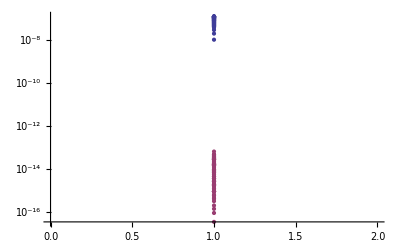

```mathematica
{runsim$maxiter,dd}/.dat//ListLogPlot
```

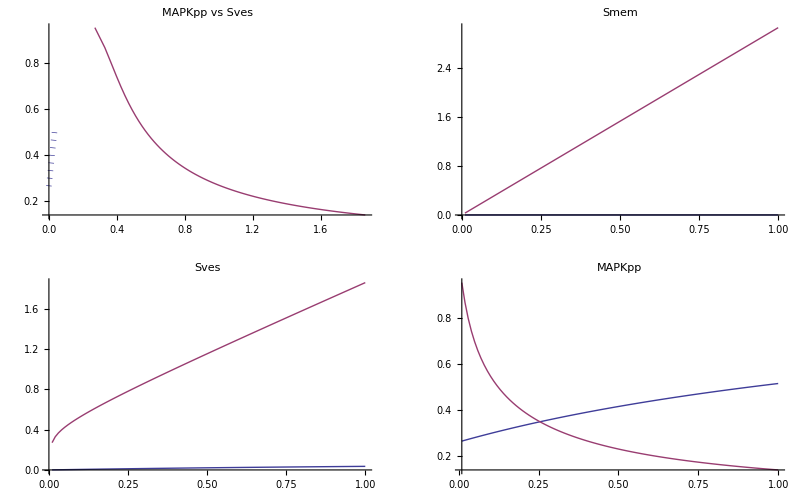

```mathematica
GraphicsGrid[{
{
ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All,AxesLabel->{}],
ListLinePlot[{δ,Smem[0]}/.dat,PlotLabel->"Smem"]
},{
ListLinePlot[{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{δ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->All]
}},ImageSize->Full]
```

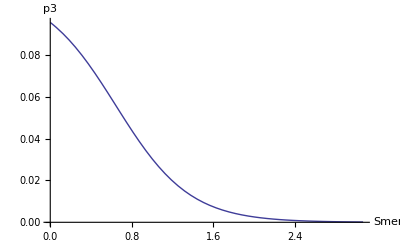

```mathematica
p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[p3c(Smem[s][t]-p3a)])+p3d]/@{0,1};
Plot[p3[0]/.p3sigmoid/.pθ/.Smem[0][t]->Smem//Evaluate,{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3b/.pθ,0},AxesLabel->{"Smem","p3"}]
```

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->d,Stot->s,p1[0]|p1[1]->p5*d,p3sigmoid}/.pθ,pθ];
runsim[plist]
,{d,dose},{s,slevel},Method->"FinestGrained"];
Dimensions[dat]
```

{2,100,66}

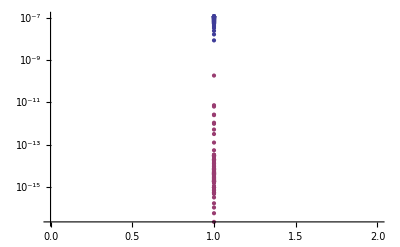

```mathematica
{runsim$maxiter,dd}/.dat//ListLogPlot
```

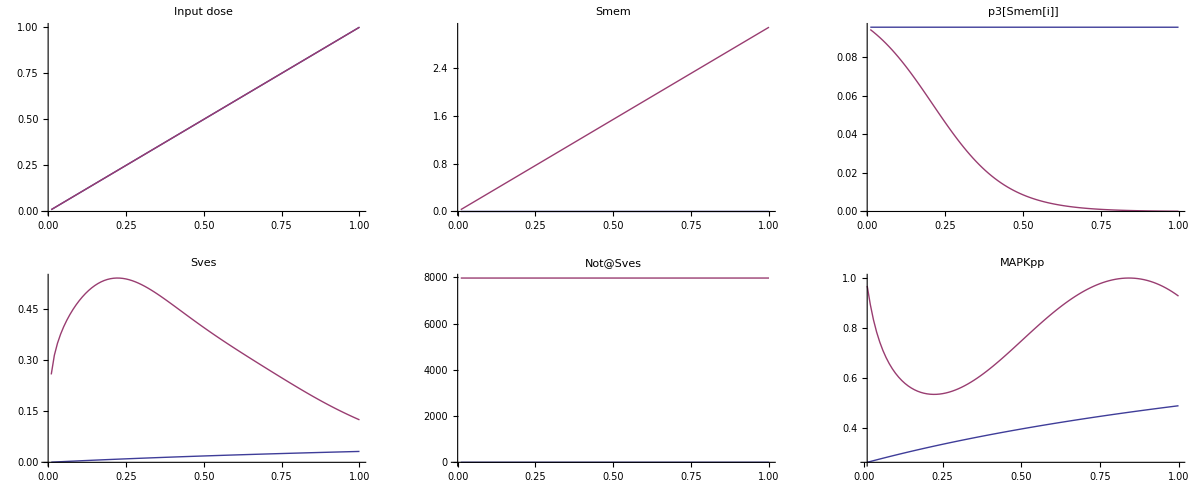

```mathematica
GraphicsGrid[{
{ListLinePlot[{δ,δ}/.dat,PlotLabel->"Input dose"],
ListLinePlot[{δ,Smem[0]}/.dat,PlotLabel->"Smem"],
ListLinePlot[{δ,p3[0]}//.(dat/.x_[t]->x),PlotLabel->"p3[Smem[i]]"]},
{ListLinePlot[{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{δ,Stot-(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Not@Sves"],
ListLinePlot[{δ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotRange->All,PlotLabel->"MAPKpp"]}
},ImageSize->Full]
```

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->d,Stot->s,p1[0]->p5*d,p1[1]->p5*(d+0.005),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{d,dose},{s,slevel},Method->"FinestGrained"];
Dimensions[dat]
```

{2,100,68}

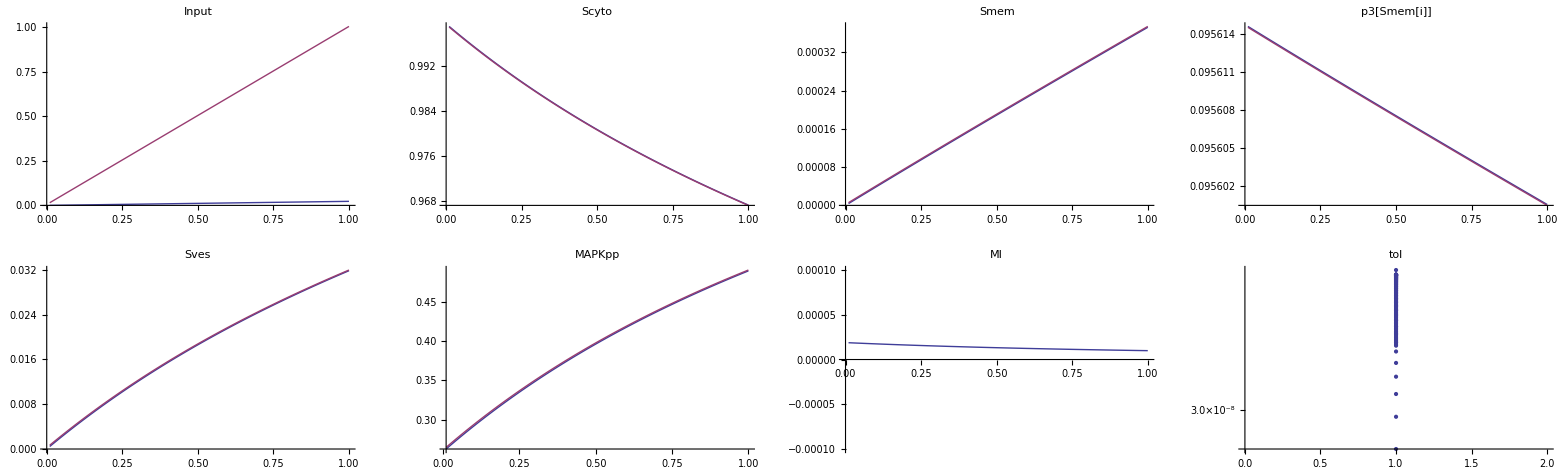

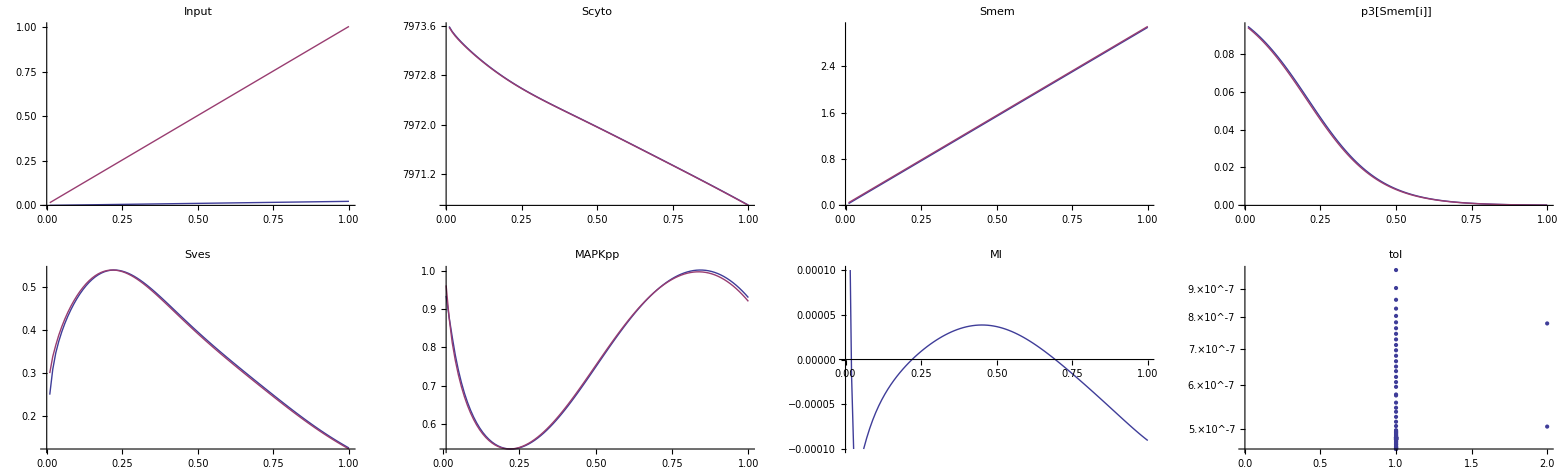

```mathematica
gf=Function[dat,
GraphicsGrid[{{
ListLinePlot[{{δ,p1[0]},{δ,p1[1]/p5}}/.dat//Transpose,PlotLabel->"Input"],
ListLinePlot[{{δ,Scyto[0]},{δ,Scyto[1]}}/.dat//Transpose,PlotLabel->"Scyto"],
ListLinePlot[{{δ,Smem[0]},{δ,Smem[1]}}/.dat//Transpose,PlotLabel->"Smem"],
ListLinePlot[{{δ,p3[0]},{δ,p3[1]}}//.dat/.x_[t]->x//Transpose,PlotLabel->"p3[Smem[i]]"]
},{
ListLinePlot[{
{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])},
{δ,(C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])}
}/.dat//Transpose,PlotLabel->"Sves"],
ListLinePlot[{{δ,MAPKpp[0]/MAXMAPKPP},{δ,MAPKpp[1]/MAXMAPKPP}}/.dat//Transpose,PlotRange->All,PlotLabel->"MAPKpp"],
ListLinePlot[{δ,MAPKpp[1]-MAPKpp[0]}/.dat,PlotRange->1 10^-4{-1,1},PlotLabel->"MI"],
ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"]
}},ImageSize->Full]];
gf[dat[[1]]]
gf[dat[[2]]]
```

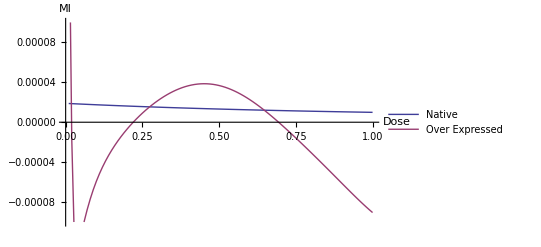

```mathematica
ListLinePlot[{δ,MAPKpp[1]-MAPKpp[0]}/.dat,PlotRange->1*10^-4{-1,1},AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Native","Over Expressed"}]]
```

### Loss

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=Module[{d,pθ=Thread[v->Abs@θ]},
dat=Transpose@ParallelTable[
plist=Join[{Stot->s,p1[0]->p5*d,p1[1]->p5*(d+0.005),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{d,dose},{s,slevel},Method->"FinestGrained"];

{MIsimNative,MIsimOE}=MAPKpp[1]-MAPKpp[0]/.dat;

MIerror=Function[{xrng,MIsim,MIuser},
d=Thread[xrng[[1]]<dose<xrng[[2]]];
Total@Abs[(MIuser/@Pick[dose,d])-Pick[MIsim,d]]
]~MapThread~{Partition[ptsuser[[All,1]],2],{MIsimNative,MIsimOE},{MIuserNative,MIuserOE}};

Total[MIerror]
]
Loss[θ0]
```

0.00105868

### FD

```mathematica
δp=10^-3;
grad=FDGradient[Loss,θ0,δp]
```

{7.8037×10^-6,-0.000607988,-0.0110687,0.000163373,-0.00021733,0.00297077,0.0161795,0.,0.}

```mathematica
Loss[θ0]//ScientificForm
```

1.54465×10^-3

Power::infy: Infinite expression 1/0. encountered.

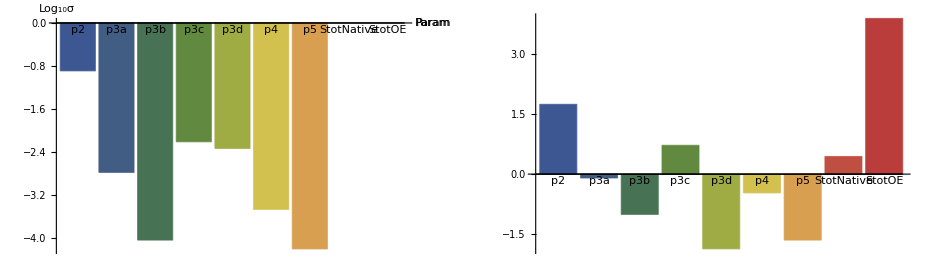

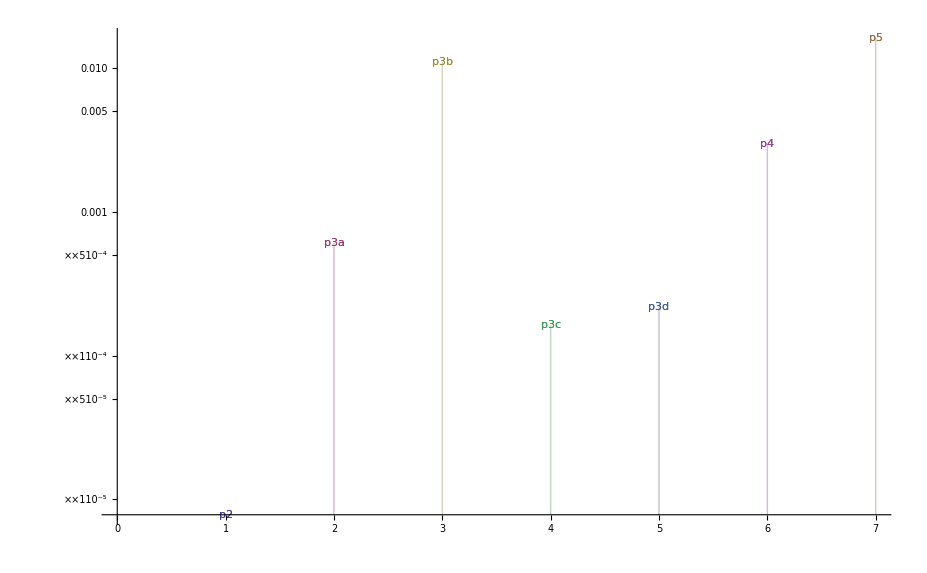

```mathematica
δL=10^-6;
σ0=δL/Abs@grad;
σ0=Clip[σ0/.ComplexInfinity->1,{0.,1}];
GraphicsRow[{
BarChart[Log[10,σ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"Param","Log_10σ"}],
BarChart[Log[10,θ0],ChartLabels->v,ChartStyle->"DarkRainbow"]}]
ListLogPlot[{Array[{#,Abs@grad[[#]]}&,Length[grad]]}ᵀ,PlotRange->All,Filling->Bottom,PlotMarkers->v]
```

```mathematica
Grid[{v,grad,σ0},Frame->All]
```

p2 | p3a | p3b | p3c | p3d | p4 | p5 | StotNative | StotOE
-0.0000667952 | -0.00244134 | 0.00449993 | 0.000190781 | -0.0275013 | -0.00124573 | 0.142117 | 7.83725×10^-7 | 1.64365×10^-12
0.0149711 | 0.000409611 | 0.000222226 | 0.00524161 | 0.000036362 | 0.000802745 | 7.03645×10^-6 | 1.27596 | 608402.

### MI user

```mathematica
xrng=dose[[{1,-1}]];
ptsuser=Thread[{xrng,0}];
ptsuser=Join[ptsuser,ptsuser]
Off[InterpolatingFunction::dmval]
```

{{0.01,0},{1.,0},{0.01,0},{1.,0}}

```mathematica
LocatorPane[Dynamic[ptsuser],
Dynamic[
{MIuserNative,MIuserOE}=Interpolation[#,InterpolationOrder->1]&/@Partition[ptsuser,2];
ListLinePlot[{
{#,MIuserNative[#]}&/@dose,{#,MIuserOE[#]}&/@dose,
{dose,MIsimNative}ᵀ,{dose,MIsimOE}ᵀ},PlotRange->{All,{-1,1}*10^-4},ImageSize->Full,PlotMarkers->Automatic,PlotStyle->{Blue,Green,Blue,Green}]
]]
```

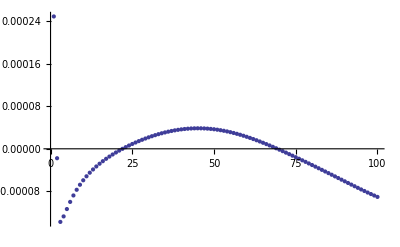

```mathematica
MIsimOE//ListPlot
```

### Opt

```mathematica
sol=.
```

0.00200497

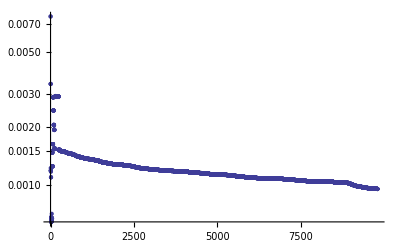

```mathematica
MyConstraints=Clip[#1,{0.0,50000}]&;
SPSAConstraints[MyConstraints];
SPSAMaxEvals[10^4]
sol=If[Head[sol]===List,
sol~Join~RandomSearch[Loss,θ0,σ0],
RandomSearch[Loss,θ0,σ0]
];
θ0=sol[[-1,2]];
Loss[θ0]
ListLogPlot[sol[[All,1]],PlotRange->All]
```

```mathematica
sol[[-1]]
```

{0.000949449,{59.069,0.642982,0.111738,2.76848,0.,0.251036,0.0227731,0.999475,7973.9}}

```mathematica
θ0=sol[[1,2]];
```

```mathematica
sol=θ0;
θ0=sol[[-1,2]]
```

{56.4362,0.733082,0.107114,4.49475,0.,0.331975,0.0230792,3.23685}

```mathematica
Loss[Last@sol[[1]]]
```

0.00143693

```mathematica
Loss[Last@sol[[-1]]]
```

0.00144529

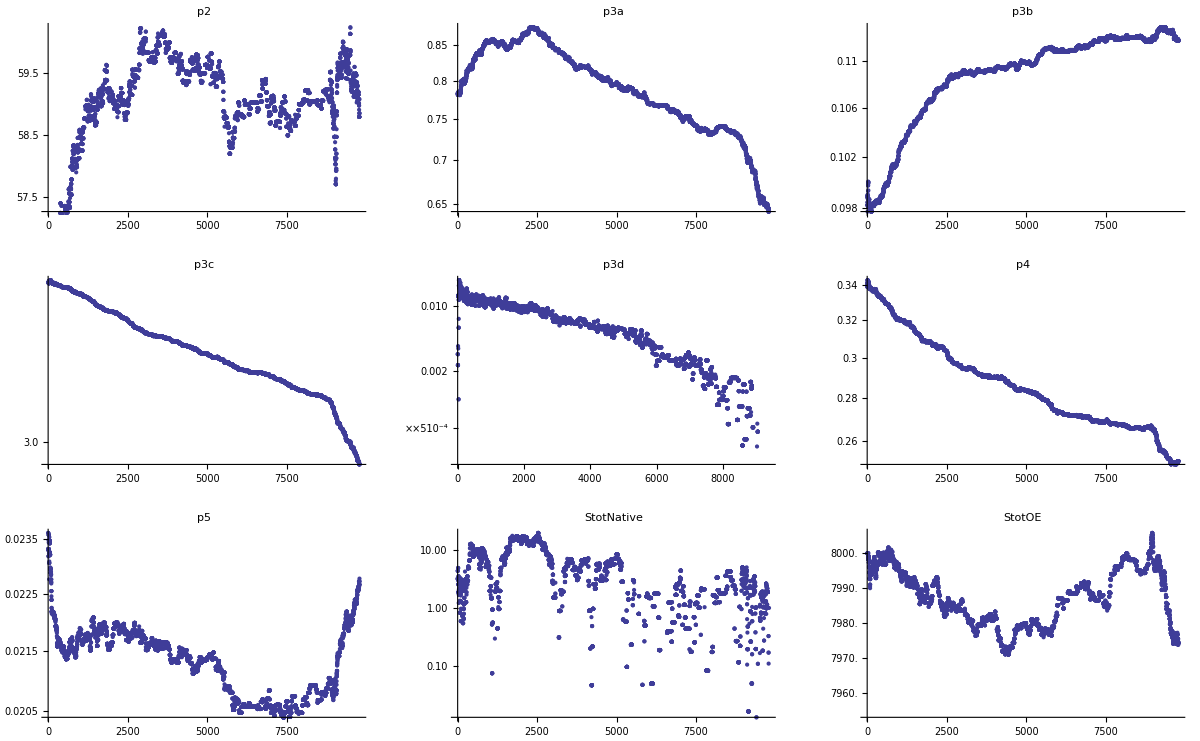

```mathematica
GraphicsGrid[MapThread[Function[{v,p},ListLogPlot[p,PlotLabel->ToString[v]]],{v,sol[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
```

```mathematica
datestr=ToString[AbsoluteTime[Round@Date[]]-AbsoluteTime[{2013,1,1,0,0,0}]]
DumpSave["/data/mapk/sol."<>datestr<>".mx",sol];
```

1775542

```mathematica
FileNames["/data/mapk/sol.*.mx"]
```

```mathematica
Get["/data/mapk/sol.mx"];
θ0=sol[[-1,2]]
```

{10.2446,0.0094522,0.0389009,220.715,0.00662966,0.675019,0.0116429,3.05658}

## θ_0

### Without using bell curve

```mathematica
θ0={8.392085459213703,0.004613100716932993,0.04061421676213222,303.73020939855957,0.005705209172238075,0.25933061784529093,0.008888869601041235,2.5868430739368926}
```

### reset

```mathematica
θ0={10.244619811558605,0.009452204414384532,0.03890094564680018,220.71529084407487,0.006629661316062501,0.6750189846410953,0.011642892596394413,3.0565806182622928}
```

### sadf

```mathematica
θ0={10.495401699076922,0.00949122005525965,0.0396108042375172,257.7856630712005,0.006134589662001442,0.6495944941256839,0.012363559034606522,3.205918289830107}
```

### double dip

```mathematica
θ0={9.979074832597293,0.029661380925632065,0.957411775253718,297.9199781493556,0.011680560536127534,0.9345840760815722,0.020749131159251055,3.044782374121911};
```

```mathematica
θ0={10.188082270746591,0.028108645398809855,0.1975968942655088,244.061865427232,0.019900265596280494,0.26402505002609894,0.020509061574344643,3.0344332682760693};
```

### this works

```mathematica
θ0={60.188082270746591,0.8,0.1975968942655088,24,0.019900265596280494,0.26402505002609894,0.020509061574344643,3.0344332682760693};
```

### even better :)

```mathematica
θ0={57.33211256761669,0.7538678260257319,0.21810743553065112,5.606942074314317,0.,0.20409181928587009,0.02242744733334517,3.1403975380183478};
```

### {2013, 1, 10, 12, 4, 4.612945`7.41655326462845}

```mathematica
θ0={56.43622167122431,0.7330821293559258,0.10711435454491272,4.494752156231409,0.,0.33197473798885224,0.02307916714522569,3.236850982008374};
```

### {2013, 1, 10, 16, 55, 13.940242`7.896845298712761}

```mathematica
θ0={56.70995318158104,0.7832247267456027,0.09889924756473911,5.292187714746446,0.000018875209270420096,0.3404435189016253,0.023315554320830257,3.231950927247027,8000};
```

## MAPK, MI vs Scaffold

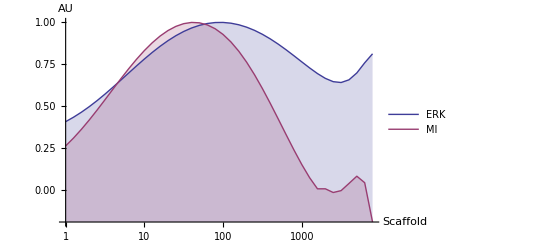

```mathematica
Begin["MIvsS`"];
dat=Transpose@ParallelTable[
plist=Join[{δ->d,Stot->StotNative*(10^s),p1[0]->p5*d,p1[1]->p5*(d+0.005),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{d,dose},Evaluate@Flatten[{s,Log[10,slevel],.1}],Method->"FinestGrained"];
Block[{MI,ERK},
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/2}/.dat//Transpose//Mean;
MI={Stot/StotNative,MAPKpp[1]-MAPKpp[0]}/.dat//Transpose//Mean;
ListLogLinearPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,Filling->Axis,AxesLabel->{"Scaffold","AU"},PlotStyle->Thick,PlotLegends->LineLegend[{"ERK","MI"}]
]
]
End[];
```

```mathematica
ListLinePlot[{δ,(MAPKpp[0]+MAPKpp[1])/2}/.dat,PlotRange->All]
```

```mathematica
Rescale
```